```mathematica
w[x_]=E^(1/v[x])/v[x];
```

```mathematica
Collect[1/v[x] w[x]^(1/2)(-v'[x]/v[x]D[(w[x]^(-1/2)f[x]), x]+v[x]D[D[(w[x]^(-1/2)f[x]), x], x]),{f''[x],f'[x],f[x]},Simplify]
```

(f'[x] v'[x])/v[x]+f''[x]+(f[x] (-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x]))/(4 v[x]^4)

```mathematica
w02[x_]=Simplify[(-v'[x]^2)/(4 v[x]^4)+v''[x]/(2 v[x]^2)+Λ/(v[x] Mp^2)/.{v''[x]->eta[x]v'[x]^2/v[x]^2}]/.v'[x]^2->2 v[x]^3/calPz[x]/Mp^2//Simplify
```

(-1+2 Λ calPz[x]+2 eta[x])/(2 Mp^2 calPz[x] v[x])

```mathematica
z2[x_]=Simplify[v'[x]^2/v[x]^2/(4w02[x])/.{v''[x]->eta[x]v'[x]^2/v[x]^2}]/.{v'[x]^2->2 v[x]^3/calPz[x]}
```

v[x]^2/(-1+2 Λ calPz[x]+2 eta[x])

```mathematica
v[x]^2/z2[x]//Expand
```

-1+2 Λ calPz[x]+2 eta[x]

```mathematica
gLf[x_]=g[x] w[x]^(1/2)(-v'[x]/v[x]D[(w[x]^(-1/2)f[x]), x]+v[x]D[D[(w[x]^(-1/2)f[x]), x], x])//Simplify
```

1/(4 v[x]^3)g[x] (-f[x] v'[x]^2-4 f[x] v[x] v'[x]^2+4 v[x]^4 f''[x]-f[x] v[x]^2 (v'[x]^2-2 v''[x])+2 v[x]^3 (2 f'[x] v'[x]+f[x] v''[x]))

```mathematica
D[gLf[x], f[x]]-D[D[gLf[x], f'[x]], x]+D[D[D[gLf[x], f''[x]], x], x]-w[x]^(1/2)(-v'[x]/v[x]D[(w[x]^(-1/2)g[x]), x]+v[x]D[D[(w[x]^(-1/2)g[x]), x], x])//Simplify
```

0

```mathematica
Normal[Series[(v''[x] v[x]^2)/v'[x]^2/.{v[x]->v0-λ/4 x^4,v'[x]->-λ x^3,v''[x]->-3λ x^2},{x,0,-1}]]
```

-(3 v0^2)/(x^4 λ)

```mathematica
(v''[x] v[x]^2)/v'[x]^2/.{v[x]->x^2,v'[x]->2x,v''[x]->2}
```

x^2/2

```mathematica
Normal[Series[(v''[x] v[x]^2)/v'[x]^2/.{v[x]->v0+g/3 x^3,v'[x]->g x^2,v''[x]->2g x},{x,0,-1}]]
```

(2 v0^2)/(g x^3)

```mathematica
Solve[{c1+c2==0,c1-c2==1},{c1,c2}]
```

{{c1→1/2,c2→-1/2}}

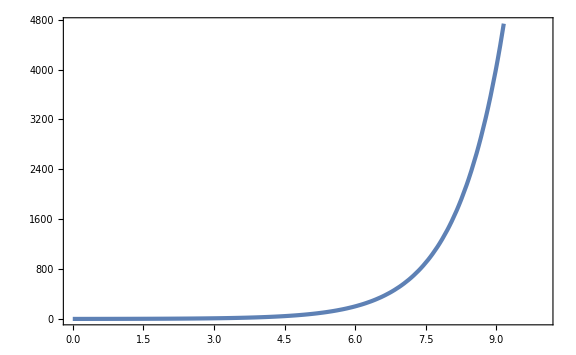

```mathematica
Plot[1/2 E^x-1/2 E^-x,{x,0,10}]
```

```mathematica
w[x_,y_]=E^(1/v[x,y])/v[x,y];
```

```mathematica
Collect[1/v[x,y] w[x,y]^(1/2)(-D[v[x,y], x]/v[x,y]D[(w[x,y]^(-1/2)f[x,y]), x]-D[v[x,y], y]/v[x,y] D[(w[x,y]^(-1/2)f[x,y]), y]+v[x,y]D[D[(w[x,y]^(-1/2)f[x,y]), x], x]+v[x,y]D[D[(w[x,y]^(-1/2)f[x,y]), y], y]),{D[D[f[x,y], x], x],D[D[f[x,y], y], y],D[f[x,y], x],D[f[x,y], y]},FullSimplify]
```

(f^(0,1)[x,y] v^(0,1)[x,y])/v[x,y]+f^(0,2)[x,y]+(f^(1,0)[x,y] v^(1,0)[x,y])/v[x,y]+f^(2,0)[x,y]+1/(4 v[x,y]^4)f[x,y] (-((1+v[x,y] (4+v[x,y])) (v^(0,1)[x,y])^2)+2 v[x,y]^2 (1+v[x,y]) v^(0,2)[x,y]-(1+v[x,y] (4+v[x,y])) (v^(1,0)[x,y])^2+2 v[x,y]^2 (1+v[x,y]) v^(2,0)[x,y])

```mathematica
1/(4 v[x,y]^4) (-(Derivative[0,1][v][x,y])^2+2 v[x,y]^2  Derivative[0,2][v][x,y]- (Derivative[1,0][v][x,y])^2+2 v[x,y]^2 Derivative[2,0][v][x,y])
```

(-(v^(0,1)[x,y])^2+2 v[x,y]^2 v^(0,2)[x,y]-(v^(1,0)[x,y])^2+2 v[x,y]^2 v^(2,0)[x,y])/(4 v[x,y]^4)

```mathematica
Collect[v'[x]^2/v[x]^3 w[x]^(1/2)(-v'[x]/v[x]D[(w[x]^(-1/2)f[x]), x]+v[x]D[D[(w[x]^(-1/2)f[x]), x], x])/.{f''[x]->D[(v[x]/v'[x] fn[x]), x],f'[x]->v[x]/v'[x] fn[x]}/.{fn'[x]->v[x]/v'[x] fnn[x]},{fnn[x],fn[x],f[x]},Simplify]
```

fnn[x]+(fn[x] (2 v'[x]^2-v[x] v''[x]))/v[x]^2+(f[x] (-((1+4 v[x]+v[x]^2) v'[x]^4)+2 v[x]^2 (1+v[x]) v'[x]^2 v''[x]))/(4 v[x]^6)

```mathematica
w02[x_]=(- v'[x]^4+2 v[x]^2  v'[x]^2 v''[x])/(4 v[x]^6)+v'[x]^2/v[x]^3 Λ/.{v''[x]->eta[x]v'[x]^2/v[x]^2}/.{v'[x]^2->2 v[x]^3/calPz[x],v'[x]^4->(2 v[x]^3/calPz[x])^2}//Simplify
```

(-1+2 Λ calPz[x]+2 eta[x])/calPz[x]^2

```mathematica
z2[x_]=(2 v'[x]^2-v[x] v''[x])/v[x]^2/(4w02[x])/.{v''[x]->eta[x]v'[x]^2/v[x]^2}/.{v'[x]^2->2 v[x]^3/calPz[x]}//Simplify
```

(calPz[x] (eta[x]-2 v[x]))/(2-4 Λ calPz[x]-4 eta[x])